#### [Calc] Deriving this Wigner distribution using linearity of Wigner transform in density operators

W1ecat  = 1/Norm[W_(α,Coh.)+W_(-α ,Coh.)+W_(+-)+W_(-+)]

W_(+-)=1/(2π)∫_(-∞)^∞ ⅇ^-ⅈpy ψ_α(x+y/2) ψ_-α*(x-y/2) ⅆy (Wikipedia convention)

```mathematica
ψ[x0_,p0_,x_]:=1/π^(1/4)ⅇ^(ⅈ p0 x)ⅇ^((-(x- x0)^2)/2)ⅇ^(-(ⅈ x0 p0)/2); (* Coherent state wave function *)
Ws1s2[α_,θ_,x_,p_,s1_,s2_]:=FullSimplify[1/(2π)∫_(-∞)^∞ ⅇ^(-ⅈ p y)ψ[s1 √2 α Cos[θ],s1 √2 α Sin[θ],x-y/2]ψ[s2 √2 α Cos[θ],-s2 √2 α Sin[θ],x+y/2]ⅆy];
```

```mathematica
Ws1s2[α,θ,x,p,1,-1]
Ws1s2[α,θ,x,p,-1,1]
```

(ⅇ^(-p^2-x^2+2 ⅈ √2 α (p Cos[θ]+x Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 ⅈ √2 α (p Cos[θ]+x Sin[θ])))/π

```mathematica
Ws1s2[α,θ,x,p,1,1]
Ws1s2[α,θ,x,p,-1,-1]
```

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (x Cos[θ]-p Sin[θ])))/π

(ⅇ^(-p^2-x^2-2 α^2+2 √2 α (-x Cos[θ]+p Sin[θ])))/π

```mathematica
FullSimplify[(Ws1s2[α,θ,x,p,1,1]+Ws1s2[α,θ,x,p,-1,-1])]
FullSimplify[(Ws1s2[α,θ,x,p,1,-1]+Ws1s2[α,θ,x,p,-1,1])]
```

(2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π

(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π

```mathematica
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));
```

#### [Calc] Finding the Wigner distribution after homodyne heralding

```mathematica
(* 
   For the current example, Wigner distribution has a form: W^(2)=1/𝒩(W_(++)+W_(--)+W_(+-)+W_(-+)).
First, we are interested in finding W_(++,--,+-,--) separately.

 Careful about using the wavefunction for coherent state here. Imaginary part ⅈrα is important.
 For conjugate: use ψ*(x0,p0;x)-> ψ(x0,-p0;x)
*)
```

```mathematica
W2modes1s2[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s1_,s2_]:=Ws1s2[ t α,θ,x1,p1,s1,s2]Ws1s2[r α,θ+π/2,x2,p2,s1,s2];
```

```mathematica
(* ++ and -- terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,-1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 r^2 α^2-2 t^2 α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))),{r^2+t^2==1}]
```

2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]

```mathematica
(* final form w_(++)+w_(--) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2-2 α^2))/π^2 2 Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]
```

```mathematica
(* +- and -+ terms for two modes *)
```

```mathematica
W2modes1s2[t,r,α,θ,x1,p1,x2,p2,1,-1]+W2modes1s2[t,r,α,θ,x1,p1,x2,p2,-1,1]
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ])))
```

```mathematica
FullSimplify[(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))),{r^2+t^2==1}]
```

2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]

```mathematica
(* final form w_(+-)+w_(-+) *)
```

```mathematica
(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2 2 Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]
```

```mathematica
(* General cat two mode B={{t, ⅈ r},{ⅈ r, t}} *)
(* Two-mode Wigner distribution just before heralding *)
W2mode[t_,r_,α_,θ_,x1_,p1_,x2_,p2_,s_]:=(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/(π^2 2(1+s ⅇ^(-2 α^2)))2 (ⅇ^(-2 α^2)Cosh[2 √2 α ((p2 r-t x1) Cos[θ]+(p1 t+r x2) Sin[θ])]+s Cos[2 √2 α ((p1 t+r x2) Cos[θ]+(-p2 r+t x1) Sin[θ])]);
```

```mathematica
int[v_,w_]:=integral@@ (v~Join~w);
(*∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-(A11 x^2+ A21 p^2+B11 x +B21 p +B121 x p +C1))ⅇ^(-(A12 x^2+ A22 p^2+B12 x +B22 p +B122 x p +C2))ⅆxⅆp*)
integral[A11_, A21_ ,B11_ ,B21_ ,B121_ , C1_,A12_, A22_ ,B12_ ,B22_ ,B122_ , C2_]:=(2 ⅇ^((B11^2+2 B11 B12+B12^2+(B11 (B121+B122)+B12 (B121+B122)-2 (A11+A12) (B21+B22))^2/(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)-4 A11 C1-4 A12 C1-4 A11 C2-4 A12 C2)/(4 (A11+A12))) π)/(√(A11+A12) √((4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)/(A11+A12)));ConditionalExpression[(2 ⅇ^((B11^2+2 B11 B12+B12^2+(B11 (B121+B122)+B12 (B121+B122)-2 (A11+A12) (B21+B22))^2/(4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)-4 A11 C1-4 A12 C1-4 A11 C2-4 A12 C2)/(4 (A11+A12))) π)/(√(A11+A12) √((4 A11 (A21+A22)+4 A12 (A21+A22)-(B121+B122)^2)/(A11+A12))), Re[(-4 A11 (A21+A22)-4 A12 (A21+A22)+(B121+B122)^2)/(A11+A12)]≤0];
```

#### Even cat

```mathematica
(* Numerator for even cat *)
ClearAll[x1,p1,x2,p2,t,r,θ,α];∫_(-∞)^∞ ((ⅇ^(-p1^2-p2^2-x1^2-x2^2-2  α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))+(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2
```

(ⅇ^(-p1^2-x1^2-x2^2-2 α^2+2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 α^2-2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2+2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 ⅈ √2 (p1 t+r x2) α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2+2 ⅈ √2 (p1 t+r x2) α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)

```mathematica
Simplify[%,r^2+t^2==1]
```

1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))+ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))+ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))))

```mathematica
(* After tracing out the momentum in mode 2 for even cat *)
Wbhnumer[t_,r_,α_,θ_,x1_,p1_,x2_]:=1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))+ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))+ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))));
```

[Calc] Checking normalization

```mathematica
ClearAll[t,r,α,Δ, θ]
∫_(-∞)^∞ Wbhnumer[t,r,α,θ, x1,p1,x2]ⅆx2
```

1/π ⅇ^(-p1^2-x1^2-2 √2 t (ⅈ p1+x1) α Cos[θ]-2 (r^2+t^2) α^2 Cos[θ]^2-2 √2 t (p1+ⅈ x1) α Sin[θ]-2 α^2 Sin[θ]^2) (ⅇ^(2 t α (t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 α (r^2 α+ⅈ √2 p1 t Cos[θ]+√2 t (2 p1+ⅈ x1) Sin[θ]))+ⅇ^(2 t α (t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (r^2 α+√2 t (ⅈ p1+2 x1) Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
Simplify[%,r^2+t^2==1]
```

1/π ⅇ^(-p1^2-x1^2-2 α^2-2 t^2 α^2-2 √2 t α ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ])) (ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 t α (2 t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (α+√2 t (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))+ⅇ^(2 α (α+√2 t ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ]))))

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ %ⅆp1ⅆx1
```

2+2 ⅇ^(-2 α^2)

```mathematica
Simplify[%,r^2+t^2==1]
```

2+2 ⅇ^(-2 α^2)

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
∫_(-Δ/2)^(Δ/2) Wbhnumer[t,r,α,θ,x1,p1,x2]ⅆx2
```

1/π^(3/2)(1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]+ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]+ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2-√2 r α Sin[θ]]+ⅇ^(2 r^2 α^2) Erf[Δ/2+√2 r α Sin[θ]])-1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]-ⅇ^(2 r^2 α^2) Erf[Δ/2-√2 r α Sin[θ]]-ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Simplify[%,r^2+t^2==1]
```

1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]));
```

```mathematica
(* Probability of success *)
∫_(-∞)^∞ ∫_(-∞)^∞ Wh[t,r,α,θ,x1,p1,Δ]ⅆx1ⅆp1
```

ⅇ^(-2 α^2) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (r^2+t^2) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

[Rslt] Wigner distributions - essential code (even cat)

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=((ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) +ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) )((Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])/(4π(1+ⅇ^(-2 α^2))))+(ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])+ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) )((Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])/(4π(1+ⅇ^(-2 α^2)))));
Ps[t_,r_,α_,θ_,Δ_]:=1/(2+2 ⅇ^(-2 α^2))ⅇ^(-2 α^2) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])) ;

WhnHomodyne[t_,r_,α_,θ_,x1_,p1_,Δ_]:=Re[Wh[t,r,α,θ,x1,p1,Δ]/Ps[t,r,α,θ,Δ]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

(* Results for the threshold detectors obtained from iPad *)
WhnThreshold[t_,r_,α_,θ_,x1_,p1_,η_]:=((Cosh[t^2 α^2]Cosh[(1-η)r^2 α^2])/Cosh[α^2(1-η r^2)])Wcat[t α,θ,x1,p1,1]+((Sinh[t^2 α^2]Sinh[(1-η)r^2 α^2])/Cosh[α^2(1-η r^2)])Wcat[t α,θ,x1,p1,-1];
PsThreshold[t_,α_,η_]:=Cosh[α^2(1-η (1-t^2))]/Cosh[α^2];

FhnThrehold[t_,r_,α_,θ_,x1_,p1_,η_]:=((Cosh[t^2 α^2]Cosh[(1-η)r^2 α^2])/Cosh[α^2(1-η r^2)])(1/(2(1+ⅇ^(-2 (t α)^2)))((ⅇ^(-p1^2-x1^2-2 (t α)^2+2 √2 (t α) (x1 Cos[θ]-p1 Sin[θ])))/π+(ⅇ^(-p1^2-x1^2-2 (t α)^2+2 √2 (t α) (-x1 Cos[θ]+p1 Sin[θ])))/π+((ⅇ^(-p1^2-x1^2+2 ⅈ √2 (t α) (p1 Cos[θ]+x1 Sin[θ])))/π+(ⅇ^(-p1^2-x1^2-2 ⅈ √2 (t α) (p1 Cos[θ]+x1 Sin[θ])))/π)))+((Sinh[t^2 α^2]Sinh[(1-η)r^2 α^2])/Cosh[α^2(1-η r^2)])(1/(2(1-ⅇ^(-2 (t α)^2)))((ⅇ^(-p1^2-x1^2-2 (t α)^2+2 √2 (t α)(x1 Cos[θ]-p1 Sin[θ])))/π+(ⅇ^(-p1^2-x1^2-2 (t α)^2+2 √2 (t α) (-x1 Cos[θ]+p1 Sin[θ])))/π-((ⅇ^(-p1^2-x1^2+2 ⅈ √2 (t α)(p1 Cos[θ]+x1 Sin[θ])))/π+(ⅇ^(-p1^2-x1^2-2 ⅈ √2 (t α) (p1 Cos[θ]+x1 Sin[θ])))/π)));
```

```mathematica
(* for a general s-cat *)
```

Fixing Δ finding η

Homodyne success probability:

0.170835

{η→0.984911}

Threshold success probability:

0.141839

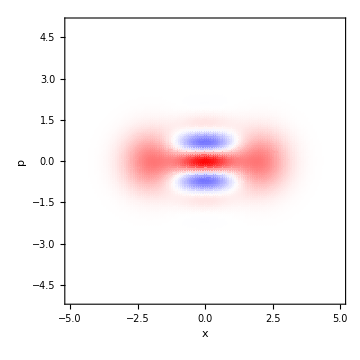
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δ,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ=0;
Δ=0.3;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

(* Psuccess *)
"Homodyne success probability: "
Re[Ps[t,√(1-t^2),α,θ,Δ]]


matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Abs[ Total[matWhHomodyne,2]](limits/range)^2);

model=WhnThreshold[t,√(1-t^2),α,θ,x,p,η];
range =(Dimensions[matWhHomodyne][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhHomodyne[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]


matWhThreshold=Table[Re[Chop[WhnThreshold[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold=matWhThreshold/(Abs[Total[matWhThreshold,2]](limits/range)^2);
"Threshold success probability: "
PsThreshold[t,α,η/.fit]

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

Comparing P_S for odd cat states w.r.t. θ

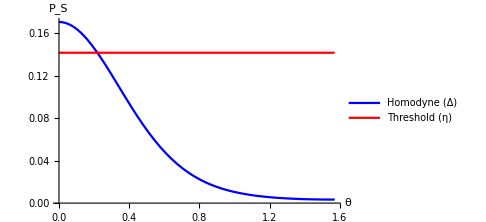

```mathematica
Plot[{Ps[t,√(1-t^2),α,θ,Δ], PsThreshold[t,α,η/.fit]},{θ,0,π/2},AxesLabel->{θ,Subscript[P, S]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->{"Homodyne (Δ)","Threshold (η)"}]
```

Fixing η  finding Δ

{Δ→0.245568}

0.000565398

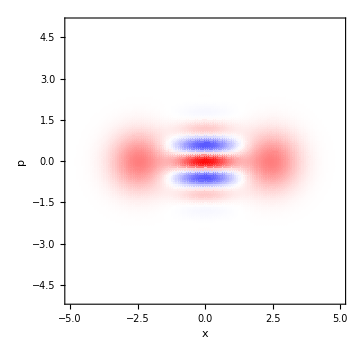
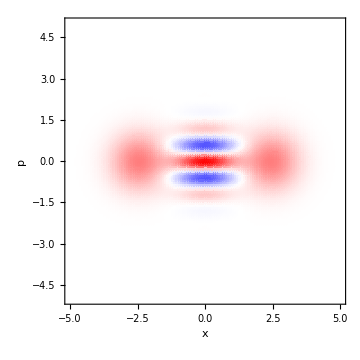
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,Δ,θ,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ =0;
η=√0.98;
t =√0.75;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

matWhThreshold=Table[Re[Chop[WhnThreshold[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold =matWhThreshold/(1+0Total[matWhThreshold,2](limits/range)^2);

model=WhnHomodyne[t,√(1-t^2),α,θ,x,p,Δ];
range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}]

Re[Ps[t,√(1-t^2),α,θ,0.001+0Δ/.fit]](* Psuccess *)

matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,√(1-t^2),α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,0.001+0Δ/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(1+0Total[matWhHomodyne,2](limits/range)^2);

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

[Calc] Absolute difference b/w W^η and W^Δ

```mathematica
ClearAll[η,Δ,t,r,θ,α,x1,x2,p1,p2];
AbsoluteDifference[η_,Δ_,t_,r_,α_,θ_]:=∫_(-∞)^∞ ∫_(-∞)^∞ Abs[Ps[t,r,α,θ,Δ]WhnThreshold[t,r,α,θ,x1,p1,η]-Wh[t,r,α,θ,x1,p1,Δ]]ⅆx1ⅆp1;
```

[Calc] Fidelity of W^η and W^Δ   : =  2π ∫∫ W^η(x, p) W^Δ(x, p) dx dp. This is problematic as it is <1 for mixed states.

```mathematica
ClearAll[η,Δ,t,r,θ,α,x1,x2,p1,p2];
Fidelity[η_,Δ_,t_,r_,α_,θ_]:=Re[(2π)/Ps[t,r,α,θ,Δ]∫_(-∞)^∞ ∫_(-∞)^∞ ((1/(4 π)ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)]))(ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])+ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]))+(1/(4 π)ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)]))(ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ])+ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])))((ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) +ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) )((Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])/(4π(1+ⅇ^(-2 α^2))))+(ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])+ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) )((Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])/(4π(1+ⅇ^(-2 α^2)))))ⅆx1ⅆp1];
```

```mathematica
Fidelity[√0.98,0.001,√0.75,√0.25,2,0]
```

```mathematica
V={((ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)]))/(4 π)),((ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)]))/(4 π)),((ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)]))/(4 π)),((ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)]))/(4 π))};
W={((Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])/(4π(1+ⅇ^(-2 α^2)))),((Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])/(4π(1+ⅇ^(-2 α^2)))),((Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])/(4π(1+ⅇ^(-2 α^2)))),((Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])/(4π(1+ⅇ^(-2 α^2))))};

ClearAll[η,Δ,t,r,α,θ];
```

```mathematica
Simplify[(2π)/1∑_(i=1)^4 ∑_(j=1)^4 V[[i]]V[[j]]int[v[i],v[j]],r^2==1-t^2]
```

```mathematica
ηPurity[η_,Δ_,t_,r_,α_,θ_]:=1/4 ⅇ^(-2 t^2 α^2) (2 ⅇ^(2 t^2 α^2)+(1+ⅇ^(4 t^2 α^2)) Cosh[2 r^2 α^2 (-1+η)]) Sech[α^2 (1-r^2 η)]^2;
```

```mathematica
Simplify[(2π)/Ps[t,r,α,θ,Δ]∑_(i=1)^4 ∑_(j=1)^4 V[[i]]W[[j]]int[v[i],w[j]],r^2==1-t^2]
```

(ⅇ^(-t^2 α^2 (5+Cos[2 θ]+ⅈ Sin[2 θ])) Sech[α^2 (1-r^2 η)] (2 ⅇ^(t^2 α^2 (6+Cos[θ]^2+2 ⅈ Cos[θ] Sin[θ]-Sin[θ]^2)) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(α^2 (2+t^2 (3 Cos[θ]^2+2 ⅈ Cos[θ] Sin[θ]+Sin[θ]^2))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(α^2 (2+t^2 (7 Cos[θ]^2+2 ⅈ Cos[θ] Sin[θ]+5 Sin[θ]^2))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(t^2 α^2 (8+Cos[θ]^2+2 ⅈ Cos[θ] Sin[θ]-Sin[θ]^2)) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+ⅇ^(t^2 α^2 (4+Cos[2 θ]+ⅈ Sin[2 θ])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+2 ⅇ^(α^2 (2+t^2 (5 Cos[θ]^2+3 Sin[θ]^2+ⅈ Sin[2 θ]))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])))/(4 (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])))

```mathematica
Fidelity[η_,Δ_,t_,r_,α_,θ_]:=Re[(ⅇ^(-t^2 α^2 (5+Cos[2 θ]+ⅈ Sin[2 θ])) Sech[α^2 (1-r^2 η)] (2 ⅇ^(t^2 α^2 (6+Cos[θ]^2-Sin[θ]^2+ⅈ Sin[2 θ])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(α^2 (2+t^2 (3 Cos[θ]^2+Sin[θ]^2+ⅈ Sin[2 θ]))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(α^2 (2+t^2 (7 Cos[θ]^2+5 Sin[θ]^2+ⅈ Sin[2 θ]))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]-Sinh[r^2 α^2 (-1+η)])+ⅇ^(t^2 α^2 (4+Cos[2 θ]+ⅈ Sin[2 θ])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+ⅇ^(t^2 α^2 (8+Cos[θ]^2-Sin[θ]^2+ⅈ Sin[2 θ])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])+2 ⅇ^(α^2 (2+t^2 (5 Cos[θ]^2+3 Sin[θ]^2+ⅈ Sin[2 θ]))) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]) (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)])))/(4 (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])))];
```

```mathematica
ηRelativeOverlap[η_,Δ_,t_,r_,α_,θ_]:=ηPurity[η,Δ,t,r,α,θ]-Fidelity[η,Δ,t,r,α,θ];
```

```mathematica
DensityPlot[HeavisideTheta[ηRelativeOverlap[η,Δ,√0.75,√0.25,10,0]],{η,0.8,1},{Δ,0,2}]
```

$Aborted

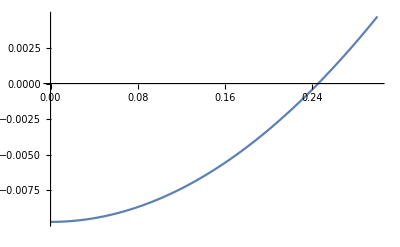

```mathematica
Plot[ηRelativeOverlap[√0.98,Δ,√0.75,√0.25,2,0],{Δ,0,0.3}]
```

```mathematica
FindRoot[ηRelativeOverlap[√0.98,Δ,√0.75,√0.25,2,0],{Δ,0.25}]
```

{Δ→0.245568}

[Rslt] Overlap = 0 on the edge

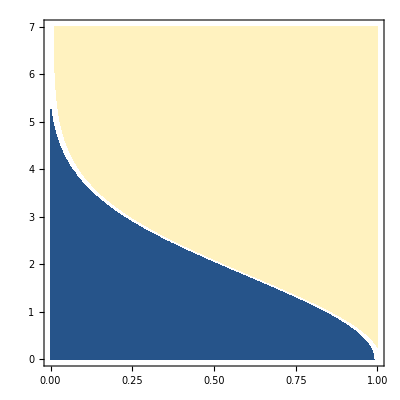

```mathematica
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) *)
v[1]=-{-1,-1,2 √2 t  α Cos[θ],-2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 t^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) *)
v[2]=-{-1,-1,-2 √2 t α Cos[θ],2 √2 t α Sin[θ],0,-2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) *)
v[3]=-{-1,-1,2 ⅈ √2 t  α Sin[θ],+2 ⅈ √2 t α Cos[θ],0,0};
(* ⅇ^(-p1^2-x1^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]) *)
v[4]=-{-1,-1,-2 ⅈ √2 t α Sin[θ],-2 ⅈ √2 t α Cos[θ],0,0};
(* ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])*)
w[1]=-{-1,-1,-2 ⅈ √2 t α Sin[θ],-2 ⅈ √2 t α Cos[θ],0,-2 α^2+2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]) *)
w[2]=-{-1,-1,2 ⅈ √2 t α Sin[θ],2 ⅈ √2 t α Cos[θ],0,-2 α^2+2 t^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) *)
w[3]=-{-1,-1,2 √2 t α Cos[θ],-2 √2  t α Sin[θ],0,-2 α^2+2 r^2 α^2};
(* ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]) *)
w[4]=-{-1,-1,-2 √2 t α Cos[θ],2 √2  t α Sin[θ],0,-2 α^2+2 r^2 α^2};
```

```mathematica
Collect[-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ],{x1,p1}]
```

-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ]

```mathematica
Simplify[ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2]))]
Simplify[ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2]))]
Simplify[ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])ⅇ^(2 r^2 α^2)]
Simplify[ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ]))]
```

ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2-2 ⅈ √2 p1 t α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ])

ⅇ^(-p1^2-x1^2-2 α^2+2 t^2 α^2+2 ⅈ √2 p1 t α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ])

ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ])

ⅇ^(-p1^2-x1^2-2 α^2+2 r^2 α^2-2 √2 t x1 α Cos[θ]+2 √2 p1 t α Sin[θ])

```mathematica
Simplify[(((Cosh[t^2 α^2]Cosh[(1-η)r^2 α^2])/(Cosh[α^2(1-η r^2)]2π(1+ⅇ^(-2 (t α)^2))))+((Sinh[t^2 α^2]Sinh[(1-η)r^2 α^2])/(Cosh[α^2(1-η r^2)]2π(1-ⅇ^(-2 (t α)^2)))))]
Simplify[(((Cosh[t^2 α^2]Cosh[(1-η)r^2 α^2])/(Cosh[α^2(1-η r^2)]2π(1+ⅇ^(-2 (t α)^2))))-((Sinh[t^2 α^2]Sinh[(1-η)r^2 α^2])/(Cosh[α^2(1-η r^2)]2π(1-ⅇ^(-2 (t α)^2)))))]
```

(ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (1-η)]))/(4 π)

(ⅇ^(t^2 α^2) Sech[α^2 (1-r^2 η)] (Cosh[r^2 α^2 (-1+η)]+Sinh[r^2 α^2 (-1+η)]))/(4 π)

#### Odd cat

```mathematica
(* Numerator for odd cat *)∫_(-∞)^∞ ((ⅇ^(-p1^2-p2^2-x1^2-x2^2-2  α^2))/π^2(ⅇ^(+2 √2 t α (x1 Cos[θ]-p1 Sin[θ])-2 √2 r α (p2 Cos[θ]+x2 Sin[θ]))+ⅇ^(+2 √2 t α (-x1 Cos[θ]+p1 Sin[θ])+2 √2 r α (p2 Cos[θ]+x2 Sin[θ])))-(ⅇ^(-p1^2-p2^2-x1^2-x2^2))/π^2(ⅇ^(-2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])-2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))+ⅇ^(+2 ⅈ √2 r α (x2 Cos[θ]-p2 Sin[θ])+2 ⅈ √2 t α (p1 Cos[θ]+x1 Sin[θ]))))ⅆp2
```

(ⅇ^(-p1^2-x1^2-x2^2-2 α^2+2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 α^2-2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2+2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2-2 ⅈ √2 (p1 t+r x2) α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2+2 ⅈ √2 (p1 t+r x2) α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)

```mathematica
Simplify[(ⅇ^(-p1^2-x1^2-x2^2-2 α^2+2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)+(ⅇ^(-p1^2-x1^2-x2^2-2 α^2-2 √2 t x1 α Cos[θ]+2 r^2 α^2 Cos[θ]^2+2 √2 (p1 t+r x2) α Sin[θ]))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2-2 ⅈ √2 (p1 t+r x2) α Cos[θ]-2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2)-(ⅇ^(-p1^2-x1^2-x2^2+2 ⅈ √2 (p1 t+r x2) α Cos[θ]+2 ⅈ √2 t x1 α Sin[θ]-2 r^2 α^2 Sin[θ]^2))/π^(3/2),{r^2+t^2==1}]
```

1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))-ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))-ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))))

```mathematica
(* After tracing out the momentum in mode 2 for odd cat *)
Wbhnumer[t_,r_,α_,θ_,x1_,p1_,x2_]:=1/π^(3/2)ⅇ^(-p1^2-x1^2-x2^2+2 √2 t x1 α Cos[θ]-2 t^2 α^2 Cos[θ]^2-2 √2 (p1 t+r x2) α Sin[θ]-2 α^2 Sin[θ]^2) (1+ⅇ^(4 √2 α (-t x1 Cos[θ]+(p1 t+r x2) Sin[θ]))-ⅇ^(2 α (t^2 α+√2 t (p1-ⅈ x1) (-ⅈ Cos[θ]+Sin[θ])+√2 r x2 (-ⅈ Cos[θ]+Sin[θ])))-ⅇ^(2 α (t^2 α+√2 t (p1+ⅈ x1) (ⅈ Cos[θ]+Sin[θ])+√2 r x2 (ⅈ Cos[θ]+Sin[θ]))));
```

[Calc] Checking normalization

```mathematica
ClearAll[t,r,α,Δ, θ]
∫_(-∞)^∞ Wbhnumer[t,r,α,θ, x1,p1,x2]ⅆx2
```

1/π ⅇ^(-p1^2-x1^2-2 √2 t (ⅈ p1+x1) α Cos[θ]-2 (r^2+t^2) α^2 Cos[θ]^2-2 √2 t (p1+ⅈ x1) α Sin[θ]-2 α^2 Sin[θ]^2) (-ⅇ^(2 t α (t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 α (r^2 α+ⅈ √2 p1 t Cos[θ]+√2 t (2 p1+ⅈ x1) Sin[θ]))-ⅇ^(2 t α (t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (r^2 α+√2 t (ⅈ p1+2 x1) Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
Simplify[1/π ⅇ^(-p1^2-x1^2-2 √2 t (ⅈ p1+x1) α Cos[θ]-2 (r^2+t^2) α^2 Cos[θ]^2-2 √2 t (p1+ⅈ x1) α Sin[θ]-2 α^2 Sin[θ]^2) (-ⅇ^(2 t α (t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))+ⅇ^(2 α (r^2 α+ⅈ √2 p1 t Cos[θ]+√2 t (2 p1+ⅈ x1) Sin[θ]))-ⅇ^(2 t α (t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (r^2 α+√2 t (ⅈ p1+2 x1) Cos[θ]+ⅈ √2 t x1 Sin[θ]))),r^2+t^2==1]
```

1/π ⅇ^(-p1^2-x1^2-2 α^2-2 t^2 α^2-2 √2 t α ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))-ⅇ^(2 t α (2 t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (α+√2 t (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))+ⅇ^(2 α (α+√2 t ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ]))))

```mathematica
∫_(-∞)^∞ (1/π ⅇ^(-p1^2-x1^2-2 α^2-2 t^2 α^2-2 √2 t α ((ⅈ p1+x1) Cos[θ]+(p1+ⅈ x1) Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+√2 p1 Sin[θ]))-ⅇ^(2 t α (2 t α+√2 (2 ⅈ p1+x1) Cos[θ]+√2 (p1+2 ⅈ x1) Sin[θ]))+ⅇ^(2 α (α+√2 t (ⅈ p1 Cos[θ]+(2 p1+ⅈ x1) Sin[θ])))+ⅇ^(2 α (α+√2 t ((ⅈ p1+2 x1) Cos[θ]+ⅈ x1 Sin[θ])))))ⅆp1
```

1/(√π)ⅇ^(-x1^2-2 α^2-3 t^2 α^2-2 √2 t x1 α Cos[θ]-t^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
Simplify[1/(√π)ⅇ^(-x1^2-2 α^2-3 t^2 α^2-2 √2 t x1 α Cos[θ]-t^2 α^2 Cos[2 θ]-2 ⅈ √2 t x1 α Sin[θ]) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ]))),r^2+t^2==1]
```

1/(√π)ⅇ^(-x1^2-2 α^2-t^2 α^2 (3+Cos[2 θ])-2 √2 t x1 α (Cos[θ]+ⅈ Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ])))

```mathematica
∫_(-∞)^∞ (1/(√π)ⅇ^(-x1^2-2 α^2-t^2 α^2 (3+Cos[2 θ])-2 √2 t x1 α (Cos[θ]+ⅈ Sin[θ])) (-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]))-ⅇ^(2 t α (2 t α+√2 x1 Cos[θ]+2 ⅈ √2 x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+ⅈ √2 t x1 Sin[θ]))+ⅇ^(2 α (α+t^2 α+2 √2 t x1 Cos[θ]+ⅈ √2 t x1 Sin[θ]))))ⅆx1
```

2-2 ⅇ^(-2 α^2)

[Calc] Heralding on Δ range in x_2 around the origin

```mathematica
(* We are leaving out the normalization 𝒩 in the denominator for now and focus on the numerator only. *)
∫_(-Δ/2)^(Δ/2) Wbhnumer[t,r,α,θ,x1,p1,x2]ⅆx2
```

1/π^(3/2)(1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]+ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2-√2 r α Sin[θ]]+ⅇ^(2 r^2 α^2) Erf[Δ/2+√2 r α Sin[θ]])-1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]-ⅇ^(2 r^2 α^2) Erf[Δ/2-√2 r α Sin[θ]]-ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Simplify[1/π^(3/2)(1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]+ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2-√2 r α Sin[θ]]+ⅇ^(2 r^2 α^2) Erf[Δ/2+√2 r α Sin[θ]])-1/2 ⅇ^(-p1^2-x1^2-α^2-r^2 α^2-t^2 α^2+2 √2 t x1 α Cos[θ]-(-1+r^2+t^2) α^2 Cos[2 θ]-2 √2 p1 t α Sin[θ]) √π (ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2-ⅈ √2 r α Cos[θ]]+ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) Erf[Δ/2+ⅈ √2 r α Cos[θ]]-ⅇ^(2 r^2 α^2) Erf[Δ/2-√2 r α Sin[θ]]-ⅇ^(2 α (r^2 α+2 √2 t (-x1 Cos[θ]+p1 Sin[θ]))) Erf[Δ/2+√2 r α Sin[θ]])),r^2+t^2==1]
```

1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]));
```

```mathematica
(* Probability of success *)
∫_(-∞)^∞ ∫_(-∞)^∞ (1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])))ⅆx1ⅆp1
```

ⅇ^(-2 α^2) (-Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]-Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (r^2+t^2) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]))

[Rslt] Wigner distributions - essential code (odd cat)

```mathematica
Wh[t_,r_,α_,θ_,x1_,p1_,Δ_]:=1/(2(1-ⅇ^(-2 α^2)))1/(2 π)ⅇ^(-p1^2-x1^2-2 α^2+2 √2 t x1 α Cos[θ]-2 √2 p1 t α Sin[θ]) (-ⅇ^(2 t α (Cos[θ/2]+ⅈ Sin[θ/2]) ((-ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1-ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])-ⅇ^(2 t α (Cos[θ/2]-ⅈ Sin[θ/2]) ((ⅈ √2 p1-√2 x1+t α) Cos[θ/2]+(√2 p1+ⅈ (√2 x1+t α)) Sin[θ/2])) (Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]+Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])])+ⅇ^(2 r^2 α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])+ⅇ^(2 α (r^2 α-2 √2 t x1 Cos[θ]+2 √2 p1 t Sin[θ])) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]]));Ps[t_,r_,α_,θ_,Δ_]:= 1/(2(1-ⅇ^(-2 α^2)))(ⅇ^(-2 α^2) (-Erf[1/2 (Δ-2 ⅈ √2 r α Cos[θ])]-Erf[1/2 (Δ+2 ⅈ √2 r α Cos[θ])]+ⅇ^(2 (r^2+t^2) α^2) (Erf[1/2 (Δ-2 √2 r α Sin[θ])]+Erf[Δ/2+√2 r α Sin[θ]])));

WhnHomodyne[t_,α_,θ_,x1_,p1_,Δ_]:=Re[Wh[t,√(1-t^2),α,θ,x1,p1,Δ]/Ps[t,√(1-t^2),α,θ,Δ]];
Wcat[α_,θ_,x_,p_,s_]:=( (2 ⅇ^(-p^2-x^2-2 α^2) Cosh[2 √2 α (x Cos[θ]-p Sin[θ])])/π+s(2 ⅇ^(-p^2-x^2) Cos[2 √2 α (p Cos[θ]+x Sin[θ])])/π)1/(2(1+s ⅇ^(-2 α^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)

(* Results for the threshold detectors obtained from iPad *)
WhnThreshold[t_,α_,θ_,x1_,p1_,η_]:=((Sinh[t^2 α^2]Cosh[(1-η)(1-t^2)α^2])/Sinh[α^2(1-η (1-t^2))])Wcat[t α,θ,x1,p1,-1]+((Cosh[t^2 α^2]Sinh[(1-η)(1-t^2)α^2])/Sinh[α^2(1-η (1-t^2))])Wcat[t α,θ,x1,p1,1];
PsThreshold[t_,α_,η_]:=Sinh[α^2(1-η (1-t^2))]/Sinh[α^2];
```

Fixing Δ finding η

Homodyne success probability:

0.165155

{η→0.984911}

Threshold success probability:

0.137123

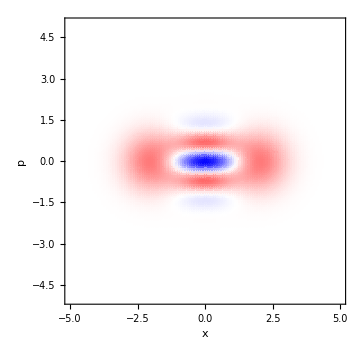
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,θ,Δ,model, fit,Data,IdxData];
limits=5;
range=60;
α=2;
θ=0π/2;
Δ=0.3;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

(* Psuccess *)
"Homodyne success probability: "
Re[Ps[t,√(1-t^2),α,θ,Δ]]


matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Abs[ Total[matWhHomodyne,2]](limits/range)^2);

model=WhnThreshold[t,α,θ,x,p,η];
range =(Dimensions[matWhHomodyne][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhHomodyne[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{η,0.5}},{p,x}]


matWhThreshold=Table[Re[Chop[WhnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold=matWhThreshold/(Abs[Total[matWhThreshold,2]](limits/range)^2);
"Threshold success probability: "
PsThreshold[t,α,η/.fit]

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```

Comparing P_S for odd cat states w.r.t. θ

```mathematica
Plot[{Ps[t,√(1-t^2),α,θ,Δ], PsThreshold[t,α,η/.fit]},{θ,0,π/2},AxesLabel->{θ,Subscript[P, S]},LabelStyle->{FontSize->20,FontFamily->"Arial",Black},AxesStyle->{{Thick,Black},{Thick,Black}},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->{"Homodyne (Δ)","Threshold (η)"}]
```

-Graphics-

Fixing η  finding Δ

{Δ→2.09067}

0.109775

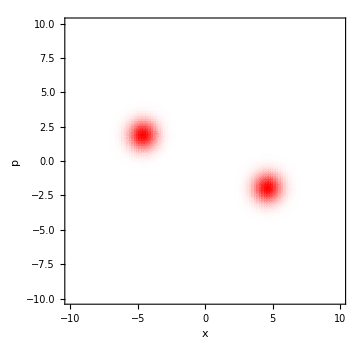
(a) Threshold | (b) Homodyne
-Graphics- | -Graphics-

```mathematica
ClearAll[η,Δ,θ,model, fit,Data,IdxData];
limits=10;
range=55;
α=5;
θ =π/8;
η=0.5;
t =√0.5;(* This is the beamsplitter transmittivity of the beamsplitter used for ZPS *)

matWhThreshold=Table[Re[Chop[WhnThreshold[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,η]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhThreshold =matWhThreshold/(Total[matWhThreshold,2](limits/range)^2);

model=WhnHomodyne[t,α,θ,x,p,Δ];
range =(Dimensions[matWhThreshold][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matWhThreshold[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,Δ,{p,x}]

Re[Ps[t,√(1-t^2),α,θ,Δ/.fit]](* Psuccess *)

matWhHomodyne=Table[Re[Chop[WhnHomodyne[t,α,θ,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits,Δ/.fit]]],{p,1,2 range +1},{x,1,2 range +1}];
matWhHomodyne =matWhHomodyne/(Total[matWhHomodyne,2](limits/range)^2);

plotThreshold=ListDensityPlot[matWhThreshold,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
plotHomodyne=ListDensityPlot[matWhHomodyne,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[matWhThreshold]],Abs[Min[matWhThreshold]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,AxesLabel->{x,p},LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium];
Grid[{{"(a) Threshold","(b) Homodyne"},{plotThreshold,plotHomodyne}}]
```